```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zack/Documents/rmtchem

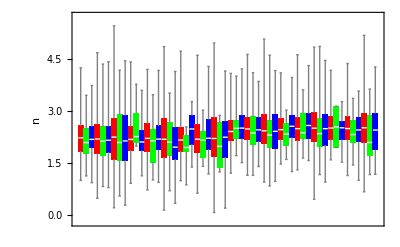

TTest::nortst: At least one of the p-values in {0.000151303,0.0119592}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.00355294,0.176136}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.0000262376,0.0265117}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

General::stop: Further output of TTest::nortst will be suppressed during this calculation.

{{{0.424349,0.678535,0.873331},{0.0173992,0.0593369,0.629295},{0.165507,0.667705,0.305069}}}

TTest::nortst: At least one of the p-values in {0.000151303,0.105368}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.00355294,0.750123}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.0000262376,0.0233199}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

General::stop: Further output of TTest::nortst will be suppressed during this calculation.

{{{0.762709,0.253179,0.463733},{0.719018,0.685248,0.011283},{0.0083891,0.0938282,0.762941}}}

TTest::nortst: At least one of the p-values in {0.0119592,0.105368}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.0265117,0.0233199}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.648411,0.00619018}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

General::stop: Further output of TTest::nortst will be suppressed during this calculation.

{{{0.59112,0.781661,0.781155},{0.0193692,0.0730249,0.246856},{0.0121734,0.244357,0.432108}}}

```mathematica
n0=Table[vals=Import["data/"<>ToString[n]<>"_"<>ToString[c]<>"_"<>ToString[d]<>".txt","Table"];Cases[vals,u_/;u[[6]]==0][[All,9]]/(n/d),{n,{50,100}},{c,{2,2.5,3}},{d,{5,10,25}}];

n1=Table[vals=Import["data/"<>ToString[n]<>"_"<>ToString[c]<>"_"<>ToString[d]<>".txt","Table"];Cases[vals,u_/;u[[6]]==1][[All,9]]/(n/d),{n,{50,100}},{c,{2,2.5,3}},{d,{5,10,25}}];
n2=Table[vals=Import["data/"<>ToString[n]<>"_"<>ToString[c]<>"_"<>ToString[d]<>".txt","Table"];Cases[vals,u_/;u[[6]]==2][[All,9]]/(n/d),{n,{50,100}},{c,{2,2.5,3}},{d,{5,10,25}}];
fn0=Flatten[n0,2];
fn1=Flatten[n1,2];
fn2=Flatten[n2,2];
BoxWhiskerChart[Flatten[Table[{fn0[[i]],fn1[[i]],fn2[[i]]},{i,1,Length[fn0]}],1],ChartStyle->{Red, Green, Blue},LabelStyle->Directive[16,Black],FrameLabel->{"",n}]

Table[TTest[{n0[[i,j,k]],n1[[i,j,k]]}],{i,1,1},{j,1,3},{k,1,3}]
Table[TTest[{n0[[i,j,k]],n2[[i,j,k]]}],{i,1,1},{j,1,3},{k,1,3}]
Table[TTest[{n1[[i,j,k]],n2[[i,j,k]]}],{i,1,1},{j,1,3},{k,1,3}]
```

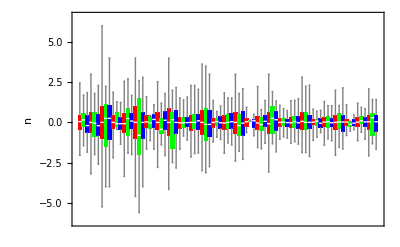

TTest::nortst: At least one of the p-values in {0.0054235,0.0523472}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.0064614,0.245547}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.0170438,0.29246}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

General::stop: Further output of TTest::nortst will be suppressed during this calculation.

{{{0.432575,0.255835,0.577004},{0.412497,0.369278,0.283257},{0.471875,0.161739,0.514375}},{{0.699825,0.361064,0.39725},{0.823638,0.645471,0.270495},{0.788831,0.278232,0.228219}},{{0.784522,0.487146,0.871108},{0.925376,0.649176,0.86208},{0.201115,0.106888,0.817891}}}

TTest::nortst: At least one of the p-values in {0.0054235,0.529763}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.0064614,0.155372}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.0170438,0.375248}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

General::stop: Further output of TTest::nortst will be suppressed during this calculation.

{{{0.137704,0.0521623,0.735834},{0.390899,0.364402,0.396939},{0.893702,0.483882,0.834672}},{{0.574558,0.312829,0.152508},{0.890184,0.158535,0.593388},{0.364062,0.314326,0.606545}},{{0.115284,0.819457,0.647056},{0.135381,0.409988,0.582445},{0.71013,0.796502,0.429951}}}

TTest::nortst: At least one of the p-values in {0.124361,0.00656169}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.00496564,0.142356}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

{{{0.148749,0.844663,0.520177},{0.207833,0.811927,0.501535},{0.510115,0.122721,0.601967}},{{0.995623,0.956095,0.990141},{0.798789,0.653941,0.574735},{0.558122,0.137991,0.456198}},{{0.189527,0.408105,0.856007},{0.465835,0.362613,0.636222},{0.271381,0.213653,0.553539}}}

```mathematica
n0=Table[vals=Import["data/"<>ToString[n]<>"_"<>ToString[c]<>"_"<>ToString[d]<>".txt","Table"];(Cases[vals,u_/;u[[6]]==0][[All,7]]-Cases[vals,u_/;u[[6]]==0][[All,8]])/(n*c/d),{n,{50,100,200}},{c,{2,2.5,3}},{d,{5,10,25}}];

n1=Table[vals=Import["data/"<>ToString[n]<>"_"<>ToString[c]<>"_"<>ToString[d]<>".txt","Table"];(Cases[vals,u_/;u[[6]]==1][[All,7]]-Cases[vals,u_/;u[[6]]==1][[All,8]])/(n*c/d),{n,{50,100,200}},{c,{2,2.5,3}},{d,{5,10,25}}];
n2=Table[vals=Import["data/"<>ToString[n]<>"_"<>ToString[c]<>"_"<>ToString[d]<>".txt","Table"];(Cases[vals,u_/;u[[6]]==2][[All,7]]-Cases[vals,u_/;u[[6]]==2][[All,8]])/(n*c/d),{n,{50,100,200}},{c,{2,2.5,3}},{d,{5,10,25}}];

fn0=Flatten[n0,2];
fn1=Flatten[n1,2];
fn2=Flatten[n2,2];BoxWhiskerChart[Flatten[Table[{fn0[[i]],fn1[[i]],fn2[[i]]},{i,1,Length[fn0]}],1],ChartStyle->{Red, Green, Blue},LabelStyle->Directive[16,Black],FrameLabel->{"",n}]
Table[TTest[{n0[[i,j,k]],n1[[i,j,k]]}],{i,1,3},{j,1,3},{k,1,3}]
Table[TTest[{n0[[i,j,k]],n2[[i,j,k]]}],{i,1,3},{j,1,3},{k,1,3}]
Table[TTest[{n1[[i,j,k]],n2[[i,j,k]]}],{i,1,3},{j,1,3},{k,1,3}]
```

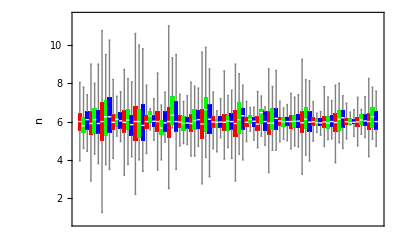

TTest::nortst: At least one of the p-values in {0.000513636,0.570929}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.107708,0.0187347}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.000439812,0.245547}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

General::stop: Further output of TTest::nortst will be suppressed during this calculation.

{{{0.211473,0.271944,0.0577933},{0.221029,0.127369,0.741309},{0.179217,0.121805,0.040104}},{{0.241862,0.129395,0.0000607118},{0.144843,0.71171,0.0696166},{0.149515,0.0271989,0.558287}},{{0.0595942,0.361407,0.00128786},{0.653112,0.895729,0.109848},{0.813939,0.192317,0.0221072}}}

TTest::nortst: At least one of the p-values in {0.000513636,0.120926}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.000439812,0.0088968}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.000761882,0.545354}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

General::stop: Further output of TTest::nortst will be suppressed during this calculation.

{{{0.162124,0.296614,0.0112587},{0.135769,0.121818,0.285906},{0.523198,0.626363,0.160278}},{{0.276323,0.000188546,0.0014281},{0.61357,0.677861,0.00916541},{0.676098,0.857328,0.178926}},{{0.6094,0.0760009,0.345175},{0.359004,0.319279,0.00544764},{0.61138,0.0393182,0.297503}}}

TTest::nortst: At least one of the p-values in {0.0187347,0.603311}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.245547,0.0088968}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

{{{0.0656396,0.751154,0.869392},{0.620599,0.0414667,0.764469},{0.283289,0.076909,0.215717}},{{0.71418,0.222226,0.0478349},{0.143519,0.554297,0.823916},{0.149178,0.151536,0.766308}},{{0.194111,0.449988,0.0309711},{0.879005,0.594532,0.73429},{0.668985,0.9963,0.221596}}}

```mathematica
n0=Table[vals=Import["data/"<>ToString[n]<>"_"<>ToString[c]<>"_"<>ToString[d]<>".txt","Table"];(Cases[vals,u_/;u[[6]]==0][[All,7]]+Cases[vals,u_/;u[[6]]==0][[All,8]])/(n/d*c),{n,{50,100,200}},{c,{2,2.5,3}},{d,{5,10,25}}];

n1=Table[vals=Import["data/"<>ToString[n]<>"_"<>ToString[c]<>"_"<>ToString[d]<>".txt","Table"];(Cases[vals,u_/;u[[6]]==1][[All,7]]+Cases[vals,u_/;u[[6]]==1][[All,8]])/(n/d*c),{n,{50,100,200}},{c,{2,2.5,3}},{d,{5,10,25}}];
n2=Table[vals=Import["data/"<>ToString[n]<>"_"<>ToString[c]<>"_"<>ToString[d]<>".txt","Table"];(Cases[vals,u_/;u[[6]]==2][[All,7]]+Cases[vals,u_/;u[[6]]==2][[All,8]])/(n/d*c),{n,{50,100,200}},{c,{2,2.5,3}},{d,{5,10,25}}];

fn0=Flatten[n0,2];
fn1=Flatten[n1,2];
fn2=Flatten[n2,2];BoxWhiskerChart[Flatten[Table[{fn0[[i]],fn1[[i]],fn2[[i]]},{i,1,Length[fn0]}],1],ChartStyle->{Red, Green, Blue},LabelStyle->Directive[16,Black],FrameLabel->{"",n}]
Table[TTest[{n0[[i,j,k]],n1[[i,j,k]]}],{i,1,3},{j,1,3},{k,1,3}]
Table[TTest[{n0[[i,j,k]],n2[[i,j,k]]}],{i,1,3},{j,1,3},{k,1,3}]
Table[TTest[{n1[[i,j,k]],n2[[i,j,k]]}],{i,1,3},{j,1,3},{k,1,3}]
```

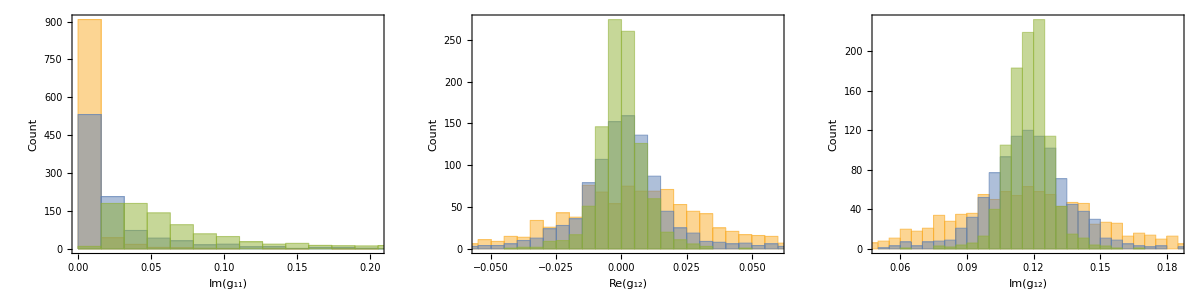
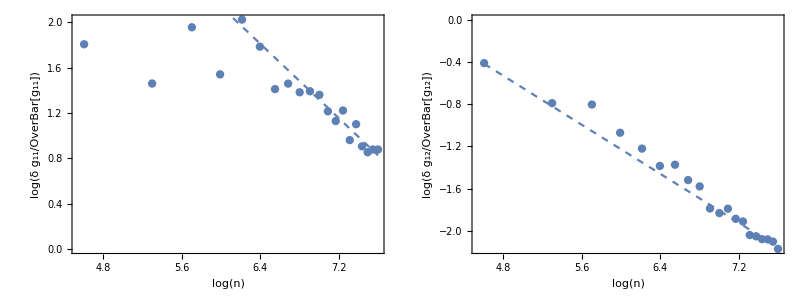

z=i.pdf

```mathematica
vals1=Partition[Partition[BinaryReadList["data/2_100_6gs.npy","Complex128"][[9;;-1]],2],2];
vals2=Partition[Partition[BinaryReadList["data/2_500_6gs.npy","Complex128"][[9;;-1]],2],2];
vals3=Partition[Partition[BinaryReadList["data/2_2000_6gs.npy","Complex128"][[9;;-1]],2],2];
p1=Grid[{{Histogram[{Im[vals1[[All,1,1]]],Im[vals2[[All,1,1]]],Im[vals3[[All,1,1]]]},Axes->False,Frame->True,FrameLabel->{Im[Subscript[g,"11"]],"Count"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->250],Histogram[{Re[vals1[[All,1,2]]],Re[vals2[[All,1,2]]],Re[vals3[[All,1,2]]]},Axes->False,Frame->True,FrameLabel->{Re[Subscript[g,"12"]],"Count"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->250],Histogram[{Im[vals1[[All,1,2]]],Im[vals2[[All,1,2]]],Im[vals3[[All,1,2]]]},Axes->False,Frame->True,FrameLabel->{Im[Subscript[g,"12"]],"Count"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->250]}}];
vals=Table[Partition[Partition[BinaryReadList["data/2_"<>ToString[n]<>"_6gs.npy","Complex128"][[9;;-1]],2],2],{n,100,2000,100}];
f1=Fit[Transpose[{Log[Table[i,{i,1000,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,1]]]^(1/2),{i,10,20}]]/Abs[Table[Mean[vals[[i,All,1,1]]],{i,10,20}]]]}],{1,x},x];
f2=Fit[Transpose[{Log[Table[i,{i,1000,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,2]]]^(1/2),{i,10,20}]]/Abs[Table[Mean[vals[[i,All,1,2]]],{i,10,20}]]]}],{1,x},x];
p2=Grid[{{Show[ListPlot[Transpose[{Log[Table[i,{i,100,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,1]]]^(1/2),{i,1,20}]]/Abs[Table[Mean[vals[[i,All,1,1]]],{i,1,20}]]]}],ImageSize->300,Axes->False,Frame->True,FrameLabel->{Log[n],Log[DisplayForm[RowBox[{δ Subscript[g,"11"],"/",OverBar[Subscript[g,"11"]]}]]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]]],Plot[f1,{x,Log[100],Log[2000]},PlotStyle->Directive[Dashed]],Epilog->{Inset[Style[f1,14],ImageScaled[{0.7,0.75}]]}],Show[ListPlot[Transpose[{Log[Table[i,{i,100,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,2]]]^(1/2),{i,1,20}]]/Abs[Table[Mean[vals[[i,All,1,2]]],{i,1,20}]]]}],ImageSize->300,Axes->False,Frame->True,FrameLabel->{Log[n],Log[DisplayForm[RowBox[{δ Subscript[g,"12"],"/",OverBar[Subscript[g,"12"]]}]]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]]],Plot[f2,{x,Log[100],Log[2000]},PlotStyle->Directive[Dashed]],Epilog->{Inset[Style[f2,14],ImageScaled[{0.7,0.75}]]}]}}];
p=Grid[{{p1},{p2}}]
Export["z=i.pdf",p]
```

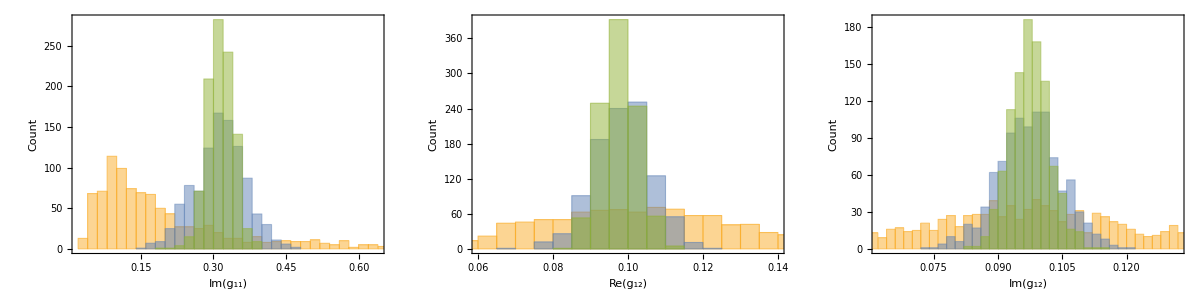
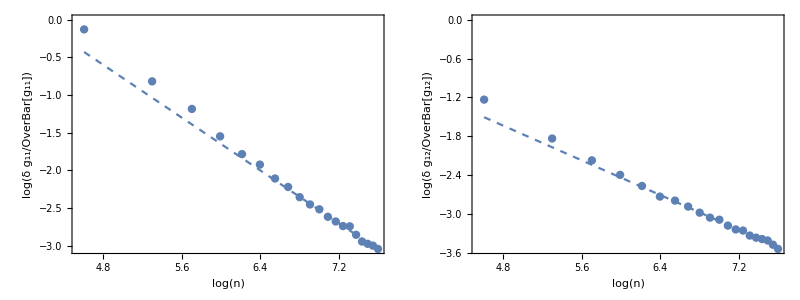

1i.pdf

```mathematica
vals1=Partition[Partition[BinaryReadList["data/2_100_3gs.npy","Complex128"][[9;;-1]],2],2];
vals2=Partition[Partition[BinaryReadList["data/2_500_3gs.npy","Complex128"][[9;;-1]],2],2];
vals3=Partition[Partition[BinaryReadList["data/2_1000_3gs.npy","Complex128"][[9;;-1]],2],2];
p1=Grid[{{Histogram[{Im[vals1[[All,1,1]]],Im[vals2[[All,1,1]]],Im[vals3[[All,1,1]]]},Axes->False,Frame->True,FrameLabel->{Im[Subscript[g,"11"]],"Count"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->250],Histogram[{Re[vals1[[All,1,2]]],Re[vals2[[All,1,2]]],Re[vals3[[All,1,2]]]},Axes->False,Frame->True,FrameLabel->{Re[Subscript[g,"12"]],"Count"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->250],Histogram[{Im[vals1[[All,1,2]]],Im[vals2[[All,1,2]]],Im[vals3[[All,1,2]]]},Axes->False,Frame->True,FrameLabel->{Im[Subscript[g,"12"]],"Count"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->250]}}];
vals=Table[Partition[Partition[BinaryReadList["data/2_"<>ToString[n]<>"_3gs.npy","Complex128"][[9;;-1]],2],2],{n,100,2000,100}];
f1=Fit[Transpose[{Log[Table[i,{i,1000,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,1]]]^(1/2),{i,10,20}]]/Abs[Table[Mean[vals[[i,All,1,1]]],{i,10,20}]]]}],{1,x},x];
f2=Fit[Transpose[{Log[Table[i,{i,1000,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,2]]]^(1/2),{i,10,20}]]/Abs[Table[Mean[vals[[i,All,1,2]]],{i,10,20}]]]}],{1,x},x];
p2=Grid[{{Show[ListPlot[Transpose[{Log[Table[i,{i,100,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,1]]]^(1/2),{i,1,20}]]/Abs[Table[Mean[vals[[i,All,1,1]]],{i,1,20}]]]}],ImageSize->300,Axes->False,Frame->True,FrameLabel->{Log[n],Log[DisplayForm[RowBox[{δ Subscript[g,"11"],"/",OverBar[Subscript[g,"11"]]}]]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]]],Plot[f1,{x,Log[100],Log[2000]},PlotStyle->Directive[Dashed]],Epilog->{Inset[Style[f1,14],ImageScaled[{0.7,0.75}]]}],Show[ListPlot[Transpose[{Log[Table[i,{i,100,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,2]]]^(1/2),{i,1,20}]]/Abs[Table[Mean[vals[[i,All,1,2]]],{i,1,20}]]]}],ImageSize->300,Axes->False,Frame->True,FrameLabel->{Log[n],Log[DisplayForm[RowBox[{δ Subscript[g,"12"],"/",OverBar[Subscript[g,"12"]]}]]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]]],Plot[f2,{x,Log[100],Log[2000]},PlotStyle->Directive[Dashed]],Epilog->{Inset[Style[f2,14],ImageScaled[{0.7,0.75}]]}]}}];
p=Grid[{{p1},{p2}}]
Export["1i.pdf",p]
```

## Regular random matrices

101

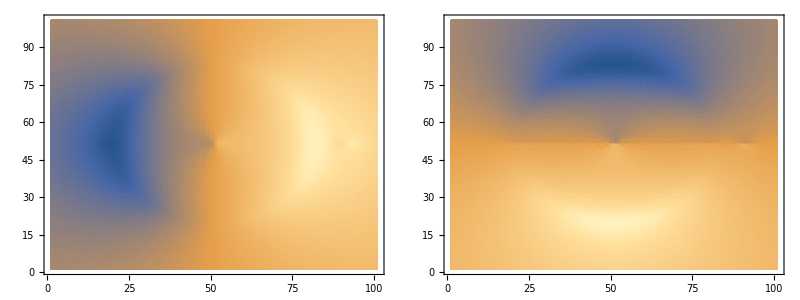

InterpolatingFunction[…]

InterpolatingFunction[…]

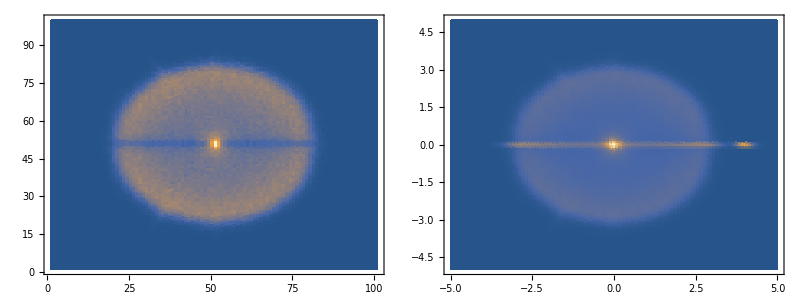

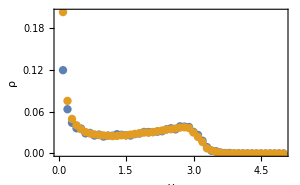

```mathematica
filebase="data/2_100_1";
n=Length[Partition[Partition[BinaryReadList[filebase<>"g.npy","Complex128"][[9;;-1]],2],2]]^(1/2)
max=5;
gvals=Partition[Partition[Partition[BinaryReadList[filebase<>"g.npy","Complex128"][[9;;-1]],2],2],n];Grid[{{ListDensityPlot[Transpose[Re[gvals[[All,All,2,1]]]],ImageSize->300,InterpolationOrder->0],
ListDensityPlot[Transpose[Im[gvals[[All,All,2,1]]]],ImageSize->300,InterpolationOrder->0]}}]
gr=Interpolation[Flatten[Table[{-max+2*max/(n-1)*(i-1),-max+2*max/(n-1)*(j-1),Re[gvals[[i,j,2,1]]]},{j,Complement[Range[n],{(n-1)/2+1}]},{i,Complement[Range[n],{(n-1)/2+1}]}],1]]
gi=Interpolation[Flatten[Table[{-max+(2*max)/(n-1)*(i-1),-max+(2*max)/(n-1)*(j-1),Im[gvals[[i,j,2,1]]]},{j,Complement[Range[n],{(n-1)/2+1}]},{i,Complement[Range[n],{(n-1)/2+1}]}],1]]

c2=Partition[BinaryReadList[filebase<>".npy","Real64"][[17;;-1]],n];
Grid[{{ListDensityPlot[Join[Transpose[c2][[1;;(n-1)/2]],Transpose[c2][[(n-1)/2+2;;n]]],ImageSize->300,InterpolationOrder->0,PlotRange->All],ListDensityPlot[Flatten[Table[{x,y,(Derivative[1,0][gr][x,y]-Derivative[0,1][gi][x,y])/(2*Pi)},{x,-max,max,2*max/n},{y,-max,max,2*max/n}],1],ImageSize->300,PlotRange->All]}}]
ListPlot[{Transpose[{max*Range[(n-1)/2]/((n-1)/2),Transpose[c2][[(n-1)/2+2;;n,(n-1)/2+1]]}],Table[{Y,Evaluate[D[gr[x,y],x]-D[gi[x,y],y]]/(2*Pi)}/.{x->0,y->Y},{Y,max/((n-1)/2),max,max/((n-1)/2)}]},ImageSize->300,InterpolationOrder->0,PlotRange->All,Axes->False,Frame->True,FrameLabel->{y,ρ},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]]]
```

data/test

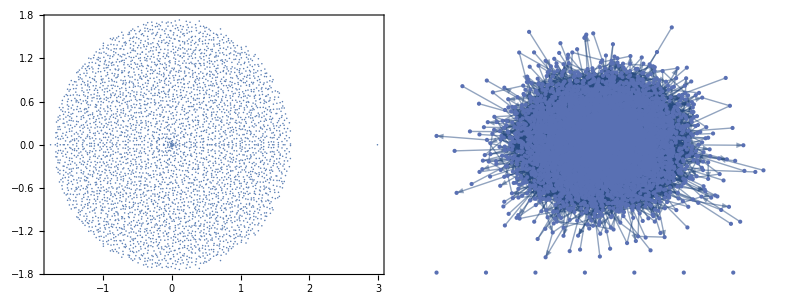

{0,10}

{0,11}

```mathematica
filebase="data/test"
mat=BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]];
n=Length[mat]^(1/2);
mat=Partition[mat,n];
evals=Partition[BinaryReadList[filebase<>"evals.npy","Real64"][[17;;-1]],2];
Grid[{{ListPlot[evals,ImageSize->300,AspectRatio->1,Axes->False,Frame->True,LabelStyle->Directive[16]],GraphPlot[AdjacencyGraph[mat/.u_/;Abs[u]>0->1/.(0.)->0],ImageSize->300]}}]
{Min[#],Max[#]}&@(Count[#,u_/;u≠0.]&/@mat)
{Min[#],Max[#]}&@(Count[#,u_/;u≠0.]&/@Transpose[mat])
```

```mathematica
Length[Length/@components]
```

571

{563.673,Null}

-Graphics-

stack.png

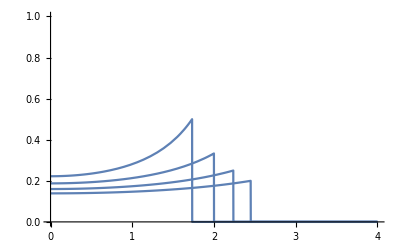

```mathematica
c2=BinaryReadList["data/2.npy","Real64"][[17;;-1]];
c2=Transpose[Partition[c2,Length[c2]^(1/2)]];
c3=BinaryReadList["data/3.npy","Real64"][[17;;-1]];
c3=Transpose[Partition[c3,Length[c3]^(1/2)]];
c4=BinaryReadList["data/4.npy","Real64"][[17;;-1]];
c4=Transpose[Partition[c4,Length[c4]^(1/2)]];
c5=BinaryReadList["data/5.npy","Real64"][[17;;-1]];
c5=Transpose[Partition[c5,Length[c5]^(1/2)]];

scale=Max[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]]/10;
offset=0.3*Median[Cases[Flatten[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]],u_/;u>100]];
cf=If[#<1,White,ColorData["M10DefaultDensityGradient"][(#-offset)/(scale-offset)]]&;
AbsoluteTiming[{raster2,raster3,raster4,raster5}={Rasterize[ListDensityPlot[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300],Rasterize[ListDensityPlot[Join[c3[[1;;Floor[Length[c3]/2]]],c3[[Floor[Length[c3]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300],Rasterize[ListDensityPlot[Join[c4[[1;;Floor[Length[c4]/2]]],c4[[Floor[Length[c4]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300],Rasterize[ListDensityPlot[Join[c5[[1;;Floor[Length[c5]/2]]],c5[[Floor[Length[c5]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300]};]
p=Rasterize[Plot3D[{0,2,4,6},{x,-10,10},{y,-10,10},Mesh->None,PlotRange->{{-8,8},{-8,8},{0,6}},PlotStyle->{Directive[Texture[raster2]],Directive[Texture[raster3]],Directive[Texture[raster4]],Directive[Texture[raster5]]},Lighting->{"Ambient",White},Boxed->False,Axes->False,Background->None,ImageSize->300,ViewPoint->{-12,0,2},AspectRatio->2,ViewAngle->0.065],ImageResolution->300];
Rotate[p,-Pi/2]
Export["stack.png",Rotate[p,-Pi/2]]
```

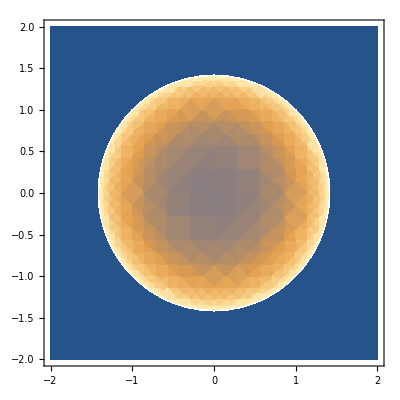

```mathematica
c=2;
DensityPlot[If[x^2+y^2<c,(c-1)*(c/(c^2-(x^2+y^2)))^2,0],{x,-c,c},{y,-c,c},PlotRange->All]
```

```mathematica
c2=BinaryReadList["data/2.npy","Real64"][[17;;-1]];
c2=Transpose[Partition[c2,Length[c2]^(1/2)]];

scale=Max[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]]/10;
offset=0.3*Median[Cases[Flatten[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]],u_/;u>100]];
cf=If[#<1,White,ColorData["M10DefaultDensityGradient"][(#-offset)/(scale-offset)]]&;

p=Rasterize[ListDensityPlot[Join[c2[[1;;Floor[Length[c2]/2]]],{c2[[Floor[Length[c2]/2]]]+c2[[2+Floor[Length[c2]/2]]]}/2,c2[[Floor[Length[c2]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->{{100,400},{100,400}},Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300]
Export["spectrum.png",p]
```

-Graphics-

spectrum.png

## Chemical reaction networks

data/test

{100,500}

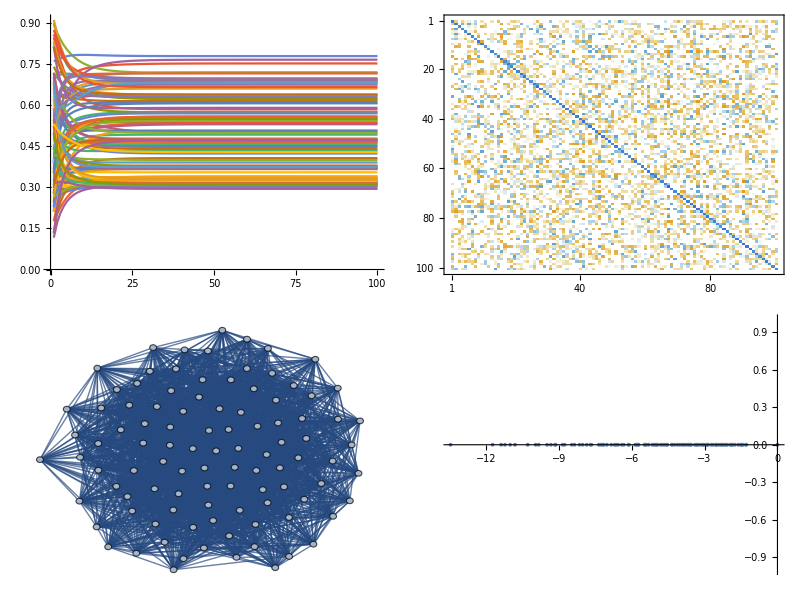

```mathematica
filebase="data/test"
{n,nr}=Import[filebase<>"out.dat"][[1]]
X=Transpose[Partition[BinaryReadList[filebase<>"X.npy","Real64"][[17;;-1]],n]];
nu=Partition[BinaryReadList[filebase<>"nu.npy","Real64"][[17;;-1]],n];
eta=Partition[BinaryReadList[filebase<>"eta.npy","Real64"][[17;;-1]],n];
mat=Partition[BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]],n];
adj=mat/.u_/;Abs[u]>0->1/.(0.)->0;
Grid[{{ListPlot[X,PlotRange->All,Joined->True,ImageSize->300],MatrixPlot[mat,ImageSize->300]},{AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300],ListPlot[{Re[#],Im[#]}&/@Eigenvalues[mat],ImageSize->300]}}]
```

data/irreversible2

{100,250}

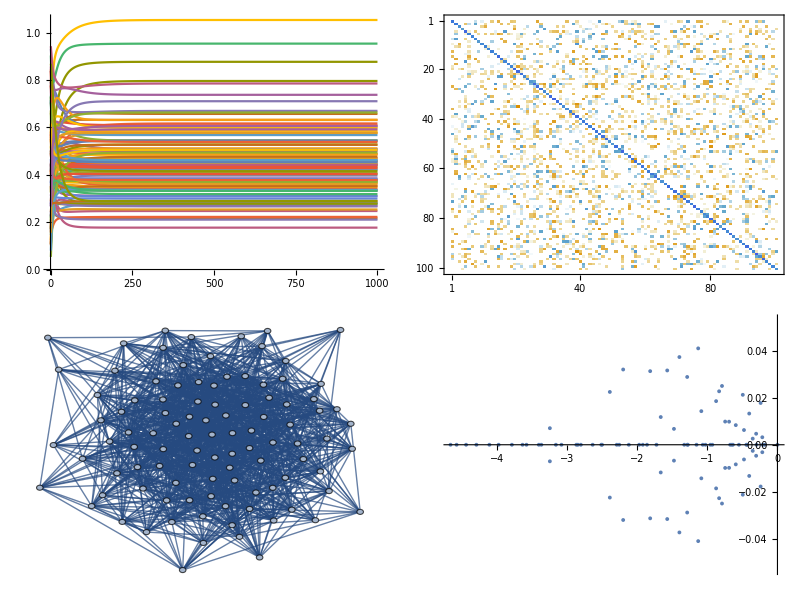

graph2.pdf

```mathematica
filebase="data/irreversible2"
{n,nr}=Import[filebase<>"out.dat"][[1]]
X=Transpose[Partition[BinaryReadList[filebase<>"X.npy","Real64"][[17;;-1]],n]];
nu=Partition[BinaryReadList[filebase<>"nu.npy","Real64"][[17;;-1]],n];
eta=Partition[BinaryReadList[filebase<>"eta.npy","Real64"][[17;;-1]],n];
mat=Partition[BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]],n];
adj=mat/.u_/;Abs[u]>0->1/.(0.)->0;
Grid[{{ListPlot[X,PlotRange->All,Joined->True,ImageSize->300],MatrixPlot[mat,ImageSize->300]},{AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300],ListPlot[{Re[#],Im[#]}&/@Eigenvalues[mat],ImageSize->300]}}]
Export["graph2.pdf",AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300]]
```

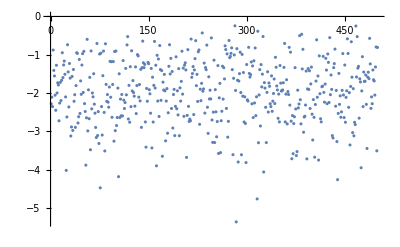

```mathematica
ListPlot[Diagonal[mat]]
```

```mathematica
filebase="data/irreversible2"
{n,nr}=Import[filebase<>"out.dat"][[1]]
X=Transpose[Partition[BinaryReadList[filebase<>"X.npy","Real64"][[17;;-1]],n]];
nu=Partition[BinaryReadList[filebase<>"nu.npy","Real64"][[17;;-1]],n];
eta=Partition[BinaryReadList[filebase<>"eta.npy","Real64"][[17;;-1]],n];
mat=Partition[BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]],n];
adj=mat/.u_/;Abs[u]>0->1/.(0.)->0;
Grid[{{ListPlot[X,PlotRange->All,Joined->True,ImageSize->300],MatrixPlot[mat,ImageSize->300]},{AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300],ListPlot[{Re[#],Im[#]}&/@Eigenvalues[mat],ImageSize->300]}}]
```

data/irreversible2

{100,250}

-Graphics-